```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Get["PlotStyles.m"]
```

/Users/yorickreum/PycharmProjects/pytorch_pde/approximator/examples/richards/results-thesis

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
```

```mathematica
OverleafPath = "/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)"
```

/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)

```mathematica
TrainingDir = "richards-2/1";
```

```mathematica
LossesData = Import[FileNameJoin[{TrainingDir,"losses.csv"}]]
```

{{0.450245282986762363},{0.410236083599297197},{0.372000754207661044},511368,{0.000210203429266087201},{0.000125561077202429697}}
 |  |  |  |

```mathematica
ListLinePlot[Flatten@LossesData, ScalingFunctions->"Log", PlotTheme->"Detailed", ImageSize->Large]
```

-Graphics-

```mathematica
LossesInterpolation = Interpolation[Flatten@LossesData, InterpolationOrder->5]
```

InterpolatingFunction[{{1.000000000000000000, 511373.000000000000}}, <>]

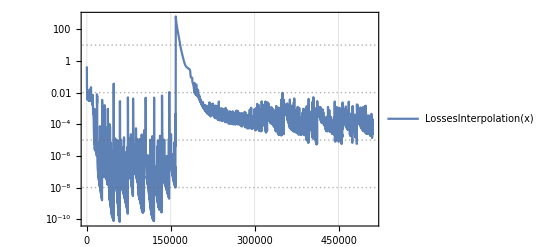

```mathematica
Plot[
LossesInterpolation[x],
Flatten@Join[{x},Rationalize@LossesInterpolation["Domain"]],
ScalingFunctions->"Log",
PlotTheme->"Detailed"
]
```